## Test Modes

```mathematica
imgsize=800;
SetDirectory@NotebookDirectory[];
```

```mathematica
Get["../../neupackage/mma/neutrino.wl"]
```

$Failed

```mathematica
Get["../../neupackage/mma/neumat.wl"]
```

$Failed

Modes

```mathematica
deltamsquare13=2.6*10^(-15);(*MeV^2*)
energy10=10;(*Energy in units of MeV*)
omegaV=OmegaVacuum[energy10,deltamsquare13](*MeV*)(*deltamsquare13/(2 energy20)(*MeV*)*)(*For 10 MeV neutrinos*)
thetaV=ArcSin[√0.093]/2
lambdaM=0.5*Cos[2thetaV]omegaV (*MeV*)
thetaM=Mod[ArcTan[Sin[2thetaV]/(Cos[2thetaV]-(lambdaN/omegaV)^2)]/2,Pi];
omegaM=OmegaMatter2[lambdaM,thetaV,omegaV](*MeV*)

endpointTest=2*10^7

twokList={1,1/200.1};
twokList2={1,1/200.2};
twoaListStash={0.02(MeVInverse2km[2Pi/(omegaM twokListKK[[1]])]/1500)^(5/3),0.02(MeVInverse2km[2Pi/(omegaM twokListKK[[2]])]/1500)^(5/3)}
twoaList={twoaListStash[[1]],twoaListStash[[2]]*300}
twoaList2={twoaList[[1]],twoaListStash[[2]]*320}
twophiList={0,0}
```

1.3×10^-16

0.154948

6.19038×10^-17

7.35104×10^-17

20000000

{0.0000112557,0.000038762}

{0.0000112557,0.0116286}

{0.0000112557,0.0124038}

{0,0}

```mathematica
?solNList
?widthNList
```

solution of a system composed of a given list of n's; Parameters taken are [listInput_,kNList_,aNList_,phiNList_,thetam_,endpoint_(*,workingprecision_:$MachinePrecision,accuracygoal_:0.5$MachinePrecision*)]

"Calculate the width; Example, widthNList[list of n's,list of k's,list of a's,list of ϕ's,thetam] and here lists are in the form {0.999,0.6,0.4}. Output is in unit of ω_m ."

Analytically, a mode is described using
P = B^2/(B^2+g^2)sin^2(q x/2)
The prediction using this equation is, for {1,0} mode

```mathematica
probTheory[nlist_,klist_,alist_,x_]:=widthNList[nlist,klist,alist,twophiList,thetaM]^2/(widthNList[nlist,klist,alist,twophiList,thetaM]^2+(nlist.klist-1)^2)Sin[x√(widthNList[nlist,klist,alist,twophiList,thetaM]^2+(nlist.klist-1)^2)/2]^2
```

```mathematica
probTheory[{1,0},twokList,twoaList,10^6]
```

0.0234696

Will the width change a lot if I modify a little bit amplitudes, due to Bessel function?

```mathematica
twoaList[[2]]/twokList[[2]]Cos[2thetaM]
```

2.14513

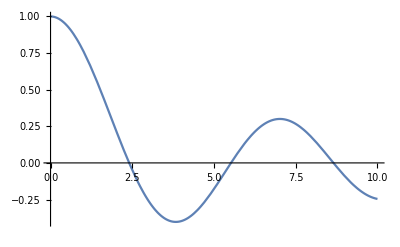

```mathematica
Plot[BesselJ[0,x],{x,0,10}]
```

```mathematica
BesselJ[0,twoaList[[2]]/twokList[[2]]Cos[2thetaM]]
BesselJ[0,twoaList2[[2]]/twokList[[2]]Cos[2thetaM]]
```

0.141071

0.0619553

```mathematica
widthNList[{1,0},twokList,twoaList,twophiList,thetaM]
widthNList[{1,0},twokList,twoaList2,twophiList,thetaM]
```

3.07607×10^-7

1.35094×10^-7

```mathematica
destructionQOrder=Part[qValueOrderdList[listNGenerator[2,10],twokList,twoaList,twophiList,thetamV],1;;10]
Grid@%
```

{{{1,0},0.},{{0,2},613.701},{{0,-2},626.093},{{0,1},841.146},{{0,-1},849.596},{{0,3},1022.48},{{0,-3},1053.61},{{0,4},2675.01},{{0,-4},2784.14},{{1,1},4049.16}}

{1,0} | 0.
{0,2} | 613.701
{0,-2} | 626.093
{0,1} | 841.146
{0,-1} | 849.596
{0,3} | 1022.48
{0,-3} | 1053.61
{0,4} | 2675.01
{0,-4} | 2784.14
{1,1} | 4049.16

```mathematica
solTest=solNList[{{1,0}},twokList,twoaList,twophiList,thetaM,endpointTest]
```

{{neumat`Private`psi1→                                 7
InterpolatingFunction[{{0., 2. 10 }}, <>],neumat`Private`psi2→                                 7
InterpolatingFunction[{{0., 2. 10 }}, <>]}}

```mathematica
solTest2=solNList[{{1,0}},twokList,twoaList2,twophiList,thetaM,endpointTest]
```

{{neumat`Private`psi1→                                 7
InterpolatingFunction[{{0., 2. 10 }}, <>],neumat`Private`psi2→                                 7
InterpolatingFunction[{{0., 2. 10 }}, <>]}}

```mathematica
solTestList=Table[{x,Abs[neumat`Private`psi2[x]]^2/.First@solTest},{x,0,endpointTest,endpointTest/1000}];
solTestList2=Table[{x,Abs[neumat`Private`psi2[x]]^2/.First@solTest2},{x,0,endpointTest,endpointTest/1000}];
theoryTestList=Table[{x,probTheory[{1,0},twokList,twoaList,x]},{x,0,endpointTest,endpointTest/1000}];
theoryTestList2=Table[{x,probTheory[{1,0},twokList,twoaList2,x]},{x,0,endpointTest,endpointTest/1000}];
```

```mathematica
ListPlot[{solTestList,solTestList2,theoryTestList,theoryTestList2},ImageSize->imgsize,Frame->True,FrameLabel->{"x̂","Transition Probability"},Joined->True,PlotStyle->{Red,Purple,{Dashing[{0.03,0.03}],Blue},{Dashing[{0.03,0.03}],{Dashing[{0.03,0.03}],Orange}}},PlotLegends->Placed[{"Numerical 10 mode (Para 1)","Numerical 10 mode (Para 2)","Theory (Para 1)","Theory (Para 2)"},{Center,Above}],Epilog->Inset["Para 1: A_2="<>ToString@twoaList[[2]]<>"\n Para 2: A_2="<>ToString@twoaList2[[2]]<>"\n Both with A_1="<>ToString@twoaList[[1]]<>"\n and {k_1,k_2}="<>ToString@twokList,{0.1,0.9},{Left,Top}],PlotLabel->"Test of Numerical and Analytical Results for Modes",LabelStyle->Black,FrameTicksStyle->Larger,BaseStyle->{FontSize->15}]
```

-Graphics-